```mathematica
data2={{{"viewing distance 57 cm"," aperture 2x2 degrees"}},{{"spatial frequency"," contrast sensitivity"}},{{0.79,96.15},{1.08,151.1},{1.77,214.1},{2.16,330.18},{3.08,523.8},{4.21,499.7},{6.14,306.22},{8.53,200.44}},{{"viewing distance 57 cm"," aperture 10x10 degrees"}},{{"spatial frequency"," contrast sensitivity"}},{{0.2,60.04},{0.27,100.79},{0.38,120.54},{0.54,200.44},{0.77,294.9},{1.06,346.1},{1.52,509.21},{2.,662.85},{3.06,580.97},{4.21,549.05},{6.14,320.98},{8.53,218.17}},{{"viewing distance 285 cm"," aperture 2x2 degrees"}},{{"spatial frequency"," contrast sensitivity"}},{{0.97,93.47},{1.35,141.46},{1.93,210.1},{2.65,398.61},{3.83,467.82},{5.38,362.79},{7.69,283.99},{10.5,208.13},{15.59,119.41},{21.28,47.},{27.45,20.14},{31.91,10.71},{35.4,6.15},{37.45,4.63},{40.77,2.58},{43.55,1.84}}};
```

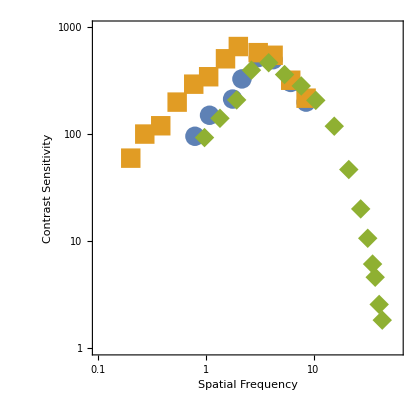

```mathematica
ListLogLogPlot[{data2[[3]],data2[[6]],data2[[9]]},PlotRange->{{.1,60},{1,1000}}, Frame->True,AspectRatio->1, FrameStyle->Directive[Black,FontSize->15,Thickness[.002]],FrameTicksStyle->{{Black,Thickness[.5]},{Black,40}},FrameTicks->{{{1,5,10,50,100,500,1000},None},{{.1,.5,1,5,10,50},None}},PlotMarkers->{Automatic,20},FrameLabel->{Style["Spatial Frequency",Black,Large],Style["Contrast Sensitivity",Black,Large]}]
```

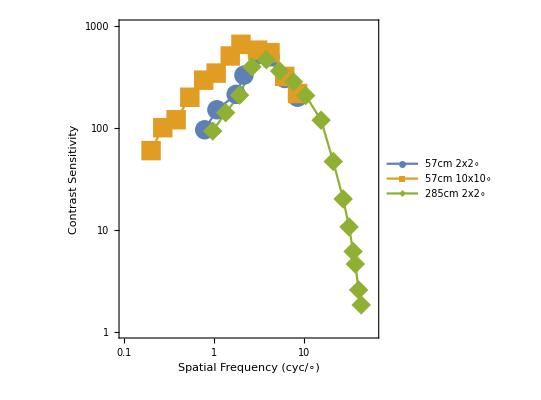

```mathematica
ListLogLogPlot[{data2[[3]],data2[[6]],data2[[9]]},PlotRange->{{.1,60},{1,1000}}, Frame->True,AspectRatio->1, FrameStyle->Directive[Black,FontSize->15,Thickness[.002]],FrameTicksStyle->{{Black,Thickness[1.5]},{Black,40}},FrameTicks->{{{1,5,10,50,100,500,1000},None},{{.1,.5,1,5,10,50},None}},PlotMarkers->{Automatic,20},FrameLabel->{Style["Spatial Frequency  (cyc/∘)",Black,Large],Style["Contrast Sensitivity",Black,Large]},Joined->True,PlotLegends->Placed[{"57cm 2x2∘","57cm 10x10∘","285cm 2x2∘"},{.4,.2}]]
```

```mathematica
Export["campbell.pdf",%]
```

campbell.pdf

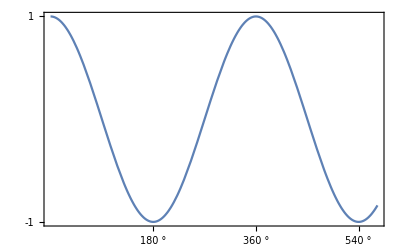

```mathematica
Plot[Cos[x],{x,0,10},Frame->True,FrameTicks->{{{Pi,180°,{0.05,0},Directive[Red,Thick]},{2Pi,360°,{.05,0},Thick},{3Pi,540°,{.05,0},Directive[Red,Dashed,Thick]}},{-1,1}}]
```

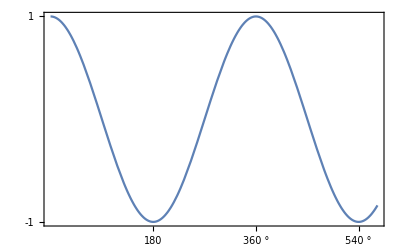

```mathematica
Plot[Cos[x],{x,0,10},Frame->True,FrameTicks->{{{Pi,180,{0.05,0},Directive[Red,Thick]},{2Pi,360°,{.05,0},Thick},{3Pi,540°,{.05,0},Directive[Red,Dashed,Thick]}},{-1,1}}]
```

#### extra

```mathematica
data={{"viewing distance 57 cm"," aperture 2x2 degrees"},{"spatial frequency"," contrast sensitivity"},{0.79,96.15},{1.08,151.1},{1.77,214.1},{2.16,330.18},{3.08,523.8},{4.21,499.7},{6.14,306.22},{8.53,200.44},{"viewing distance 57 cm"," aperture 10x10 degrees"},{"spatial frequency"," contrast sensitivity"},{0.2,60.04},{0.27,100.79},{0.38,120.54},{0.54,200.44},{0.77,294.9},{1.06,346.1},{1.52,509.21},{2.,662.85},{3.06,580.97},{4.21,549.05},{6.14,320.98},{8.53,218.17},{"viewing distance 285 cm"," aperture 2x2 degrees"},{"spatial frequency"," contrast sensitivity"},{0.97,93.47},{1.35,141.46},{1.93,210.1},{2.65,398.61},{3.83,467.82},{5.38,362.79},{7.69,283.99},{10.5,208.13},{15.59,119.41},{21.28,47.},{27.45,20.14},{31.91,10.71},{35.4,6.15},{37.45,4.63},{40.77,2.58},{43.55,1.84}}
```

{{viewing distance 57 cm, aperture 2x2 degrees},{spatial frequency, contrast sensitivity},{0.79,96.15},{1.08,151.1},{1.77,214.1},{2.16,330.18},{3.08,523.8},{4.21,499.7},{6.14,306.22},{8.53,200.44},{viewing distance 57 cm, aperture 10x10 degrees},{spatial frequency, contrast sensitivity},{0.2,60.04},{0.27,100.79},{0.38,120.54},{0.54,200.44},{0.77,294.9},{1.06,346.1},{1.52,509.21},{2.,662.85},{3.06,580.97},{4.21,549.05},{6.14,320.98},{8.53,218.17},{viewing distance 285 cm, aperture 2x2 degrees},{spatial frequency, contrast sensitivity},{0.97,93.47},{1.35,141.46},{1.93,210.1},{2.65,398.61},{3.83,467.82},{5.38,362.79},{7.69,283.99},{10.5,208.13},{15.59,119.41},{21.28,47.},{27.45,20.14},{31.91,10.71},{35.4,6.15},{37.45,4.63},{40.77,2.58},{43.55,1.84}}

```mathematica
ListLogLogPlot[{data2[[3]],data2[[6]],data2[[9]]},PlotRange->{{.1,60},{1,1000}}, Frame->True,AspectRatio->1, FrameStyle->Directive[Black,FontSize->15,Thickness[.002]],FrameTicksStyle->{{Red,Thickness[.5]},{Black,40}},PlotMarkers->{Automatic,20},FrameLabel->{Style["Spatial Frequency",Black,Large],Style["Contrast Sensitivity",Black,Large]}];
```

```mathematica
FrameTicks->{{{0.5,50,1},None},{{5,100,1000},None}}

FrameTicks->{{{0,0°,.6},{Pi,180°,.2},{2Pi,360°,.2},{3Pi,540°,.2}},{-1/2,1/2}}
```

FrameTicks→{{{0.5,50,1},None},{{5,100,1000},None}}

FrameTicks→{{{0,0,0.6},{π,180 °,0.2},{2 π,360 °,0.2},{3 π,540 °,0.2}},{-1/2,1/2}}

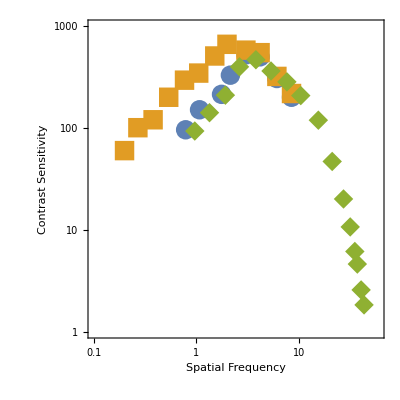

```mathematica
ListLogLogPlot[{data2[[3]],data2[[6]],data2[[9]]},PlotRange->{{.1,60},{1,1000}}, Frame->True,AspectRatio->1, FrameStyle->Directive[Black,FontSize->15,Thickness[.002]],FrameTicksStyle->{{Black,Thickness[.5]},{Black,40}},PlotMarkers->{Automatic,20},FrameLabel->{Style["Spatial Frequency",Black,Large],Style["Contrast Sensitivity",Black,Large]}]
```